## Solving equations

### Algebraic equations

```mathematica
f[x_,a_]:=2 x^2+2-a
```

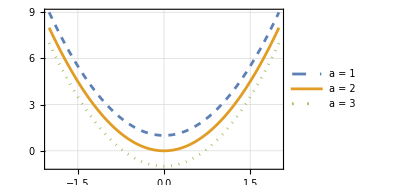

```mathematica
plotfa=Plot[{f[x,1],f[x,2],f[x,3]} , {x, -2,2},
PlotStyle->{Dashed,Default,Dotted},
PlotTheme->"Detailed",ImageSize->300,
PlotLegends->Placed[ {"a = 1","a = 2","a = 3"}, Center]
]
```

```mathematica
Export[NotebookDirectory[]<>"pics/06-plotfa.pdf",plotfa]
```

/home/jam/Kuweta/mma_lessons/code/pics/06-plotfa.pdf

```mathematica
solutions=Solve[f[x,a] ==0 , x]
```

{{x→-(√(-2+a))/(√2)},{x→(√(-2+a))/(√2)}}

```mathematica
ReplaceAll[f[x,a],solutions]
```

{0,0}

```mathematica
f[x,a]/. solutions
```

{0,0}

### Non-polynomial equations

```mathematica
Solve[E^x==2,x,Reals]
```

{{x→Log[2]}}

```mathematica
Solve[E^x==2,x,Complexes]
```

{{x→ConditionalExpression[2 ⅈ π C[1]+Log[2], C[1]∈ℤ]}}

```mathematica
Solve[E^x==2,x,Integers]
```

{}

```mathematica
Solve[Exp[x]==1,x]
```

{{x→ConditionalExpression[2 ⅈ π C[1], C[1]∈ℤ]}}

```mathematica
Solve[Exp[x]==2,x, Complexes]
```

{{x→ConditionalExpression[2 ⅈ π C[1]+Log[2], C[1]∈ℤ]}}

```mathematica
Solve[Exp[x]==2,x, Reals]
```

{{x→Log[2]}}

```mathematica
Solve[Exp[x]==2,x, Integers]
```

{}

```mathematica
Solve[x+Exp[x]==1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0}}

```mathematica
Solve[x+Exp[x]==1,x∈Complexes]
```

{{x→0},{x→ConditionalExpression[1-ProductLog[C[1],ⅇ], C[1]∈ℤ]}}

```mathematica
Solve[x+Exp[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-ProductLog[1]}}

```mathematica
ProductLog[1]//N
```

0.567143

### Numerical solutions

```mathematica
NSolve[f[x,a] ==0 , x]
```

{{x→-0.707107 √(-2.+a)},{x→0.707107 √(-2.+a)}}

```mathematica
FindRoot[f[x,2],{x,0}]
```

{x→0.}

```mathematica
FindRoot[f[x,0],{x,0}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.}. Try perturbing the initial point(s).

{x→0.}

```mathematica
FindRoot[f[x,0],{x,2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→-2.3798×10^-6}

```mathematica
NSolve[x+Exp[x]==1,x]
```

{{x→0.}}

```mathematica
NSolve[x+Exp[x]==0,x]
```

{{x→-0.567143},{x→1.53391+4.37519 ⅈ},{x→2.40159+10.7763 ⅈ},{x→2.85358+17.1135 ⅈ},{x→3.16295+23.4277 ⅈ},{x→3.39869+29.7313 ⅈ},{x→3.58926+36.029 ⅈ},{x→3.74924+42.3231 ⅈ},{x→3.88712+48.6149 ⅈ},{x→4.00826+54.905 ⅈ},{x→4.1163+61.1939 ⅈ},{x→4.2138+67.4819 ⅈ},{x→4.30264+73.7692 ⅈ},{x→4.38422+80.0559 ⅈ},{x→4.45965+86.3422 ⅈ},{x→4.52979+92.6281 ⅈ}}

```mathematica
FindRoot[Exp[x]+x,{x,-100}]
```

{x→-0.567143}

### Plotting solutions

```mathematica
Clear[g]
```

```mathematica
g[x_]:=x^4-x^3-x^2+1
```

```mathematica
Solve[g[x] ==0,x]
```

{{x→1},{x→Root1.32Root[-1-#1+#1^3&,1]1.324717957244746},{x→Root-0.662-0.562 ⅈRoot[-1-#1+#1^3&,2]-0.662358978622373},{x→Root-0.662+0.562 ⅈRoot[-1-#1+#1^3&,3]-0.662358978622373}}

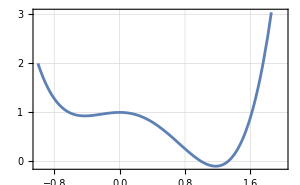

```mathematica
plotg=Plot[g[x],{x,-1,2},PlotTheme->"Detailed",PlotLegends->None,ImageSize->300]
```

```mathematica
Export[NotebookDirectory[]<>"pics/06-plotg.pdf",plotg]
```

/home/jam/Kuweta/mma_lessons/code/pics/06-plotg.pdf

```mathematica
Solve[g[x]==0,x,Reals]
```

{{x→1},{x→Root1.32Root[-1-#1+#1^3&,1]1.324717957244746}}

```mathematica
Solve[g[x]==0,x,Cubics->True]
```

{{x→1},{x→1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3)},{x→-1/6 (1+ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1-ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))},{x→-1/6 (1-ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1+ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))}}

## Systems of equations

```mathematica
Clear[x1,x2,a1,a2,a3,a4]
Solve[{a1 x1 +a2 x2 ==c1,a3 x1 + a4 x2 == c2},{x1, x2}]
```

{{x1→-(a4 c1-a2 c2)/(a2 a3-a1 a4),x2→-(-a3 c1+a1 c2)/(a2 a3-a1 a4)}}

```mathematica
mA = Table[Subscript[α, i,j],{i,1,3},{j,1,3}]
```

{{α_(1,1),α_(1,2),α_(1,3)},{α_(2,1),α_(2,2),α_(2,3)},{α_(3,1),α_(3,2),α_(3,3)}}

```mathematica
b=Table[Subscript[β, i],{i,1,3}]
```

{β_1,β_2,β_3}

```mathematica
LinearSolve[mA,b]
```

{(β_3 α_(1,3) α_(2,2)-β_3 α_(1,2) α_(2,3)-β_2 α_(1,3) α_(3,2)+β_1 α_(2,3) α_(3,2)+β_2 α_(1,2) α_(3,3)-β_1 α_(2,2) α_(3,3))/(α_(1,3) α_(2,2) α_(3,1)-α_(1,2) α_(2,3) α_(3,1)-α_(1,3) α_(2,1) α_(3,2)+α_(1,1) α_(2,3) α_(3,2)+α_(1,2) α_(2,1) α_(3,3)-α_(1,1) α_(2,2) α_(3,3)),(β_3 α_(1,3) α_(2,1)-β_3 α_(1,1) α_(2,3)-β_2 α_(1,3) α_(3,1)+β_1 α_(2,3) α_(3,1)+β_2 α_(1,1) α_(3,3)-β_1 α_(2,1) α_(3,3))/(-α_(1,3) α_(2,2) α_(3,1)+α_(1,2) α_(2,3) α_(3,1)+α_(1,3) α_(2,1) α_(3,2)-α_(1,1) α_(2,3) α_(3,2)-α_(1,2) α_(2,1) α_(3,3)+α_(1,1) α_(2,2) α_(3,3)),(β_3 α_(1,2) α_(2,1)-β_3 α_(1,1) α_(2,2)-β_2 α_(1,2) α_(3,1)+β_1 α_(2,2) α_(3,1)+β_2 α_(1,1) α_(3,2)-β_1 α_(2,1) α_(3,2))/(α_(1,3) α_(2,2) α_(3,1)-α_(1,2) α_(2,3) α_(3,1)-α_(1,3) α_(2,1) α_(3,2)+α_(1,1) α_(2,3) α_(3,2)+α_(1,2) α_(2,1) α_(3,3)-α_(1,1) α_(2,2) α_(3,3))}

```mathematica
x=Table[Subscript[ξ, i],{i,1,3}]
```

{ξ_1,ξ_2,ξ_3}

```mathematica
Solve[mA.x==b,x]
```

{{ξ_1→-(-β_3 α_(1,3) α_(2,2)+β_3 α_(1,2) α_(2,3)+β_2 α_(1,3) α_(3,2)-β_1 α_(2,3) α_(3,2)-β_2 α_(1,2) α_(3,3)+β_1 α_(2,2) α_(3,3))/(α_(1,3) α_(2,2) α_(3,1)-α_(1,2) α_(2,3) α_(3,1)-α_(1,3) α_(2,1) α_(3,2)+α_(1,1) α_(2,3) α_(3,2)+α_(1,2) α_(2,1) α_(3,3)-α_(1,1) α_(2,2) α_(3,3)),ξ_2→-(β_3 α_(1,3) α_(2,1)-β_3 α_(1,1) α_(2,3)-β_2 α_(1,3) α_(3,1)+β_1 α_(2,3) α_(3,1)+β_2 α_(1,1) α_(3,3)-β_1 α_(2,1) α_(3,3))/(α_(1,3) α_(2,2) α_(3,1)-α_(1,2) α_(2,3) α_(3,1)-α_(1,3) α_(2,1) α_(3,2)+α_(1,1) α_(2,3) α_(3,2)+α_(1,2) α_(2,1) α_(3,3)-α_(1,1) α_(2,2) α_(3,3)),ξ_3→-(β_3 α_(1,2) α_(2,1)-β_3 α_(1,1) α_(2,2)-β_2 α_(1,2) α_(3,1)+β_1 α_(2,2) α_(3,1)+β_2 α_(1,1) α_(3,2)-β_1 α_(2,1) α_(3,2))/(-α_(1,3) α_(2,2) α_(3,1)+α_(1,2) α_(2,3) α_(3,1)+α_(1,3) α_(2,1) α_(3,2)-α_(1,1) α_(2,3) α_(3,2)-α_(1,2) α_(2,1) α_(3,3)+α_(1,1) α_(2,2) α_(3,3))}}

### Differential equations

```mathematica
Clear[x,f]
DSolve[f'[x]==f[x],f,x]
```

{{f→Function[{x},ⅇ^x C[1]]}}

```mathematica
Clear[f]
```

```mathematica
ndsol=NDSolve[{f'[x]==f[x],f[0]==0.1},f,{x,0,10}]
```

{{f→InterpolatingFunction[…]}}

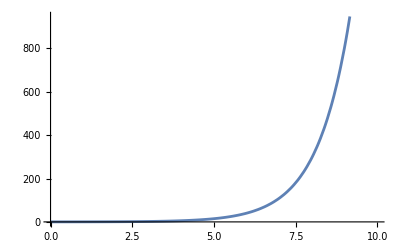

```mathematica
Plot[f[x]/.ndsol,{x,0,10}]
```

### Recurrence equations

```mathematica
Clear[T];
ans=RSolve[{T[n]==2 T[n-1]+1,T[0]==0},T[n],n]
```

{{T[n]→-1+2^n}}

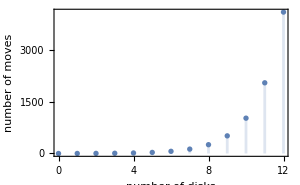

```mathematica
tohPlot=DiscretePlot[T[n]/.ans[[1]],{n,0,12},PlotRange->All,Frame->True,FrameLabel->{"number of disks","number of moves"},ImageSize->300]
```

```mathematica
Export[NotebookDirectory[]<>"pics/06-towers-of-hanoi.pdf",tohPlot]
```

/home/jam/Kuweta/mma_lessons/code/pics/06-towers-of-hanoi.pdf

```mathematica
Clear[T];
fans=RSolve[{T[n+1]==2 T[n]+1,T[0]==0},T,n]
```

{{T→Function[{n},-1+2^n]}}

```mathematica
T/.fans[[1]]
```

Function[{n},-1+2^n]

```mathematica
(T/. fans[[1]])[64]
```

18446744073709551615

```mathematica
RSolveValue[{T[n + 1] == 2  T[n] + 1, T[0] == 0}, T, n]
```

Function[{n},-1+2^n]

```mathematica
RSolveValue[{T[n+1]==2  T[n]+1,T[0]==0},T[n],n]
```

-1+2^n